#### Define two vectors A and B. Use curly braces to enclose the vector components

Define A

```mathematica
A={1,2,-4}
```

{1,2,-4}

Define B

```mathematica
B={-2,1,3}
```

{-2,1,3}

#### Vector addition

```mathematica
A+B
```

{-1,3,-1}

```mathematica
2 A + 7 B
```

{-12,11,13}

```mathematica
α A + β B
```

{α-2 β,2 α+β,3 β-4 α}

#### Dot product

```mathematica
A.B
```

-12

```mathematica
X={3,4,1}
```

{3,4,1}

```mathematica
A.(α B + β X)
```

-4 (3 α+β)+2 (α+4 β)-2 α+3 β

#### Cross product

```mathematica
Cross[A,B]
```

{10,5,5}

#### Be careful to use spaces in multiplication

```mathematica
3A - β B
```

{2 β+3,6-β,-3 β-12}

```mathematica
3A - βB (* Notice no space between β and B *)
```

{3-βB,6-βB,-βB-12}

With space

```mathematica
x y
```

x y

without space

```mathematica
xy
```

xy

```mathematica
Cos[ω t]
```

cos(t ω)

```mathematica
Cos[ωt]
```

cos(ωt)

#### Compute magnitude of A

```mathematica
Norm[A]
```

√21

```mathematica
Sqrt[A.A]
```

√21

Result is exact (not a rounded decimal approximation)

#### To get a numerical approximation, use the N[ ] function

```mathematica
N[Sqrt[A.A],100]
```

4.582575694955840006588047193728008488984456576767971902607242123906868425547770886604361559493445033

```mathematica
N[Pi,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

#### Use square brackets for function calls. All built-in function names are capitalized.

```mathematica
Cos[ω t]
```

cos(t ω)

```mathematica
cos[ω t] (* Not defined! *)
```

cos(t ω)

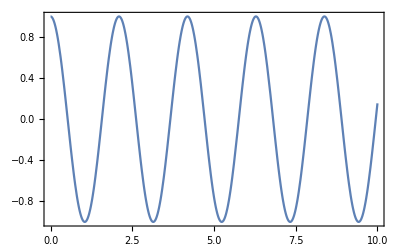

```mathematica
Plot[Cos[3t],{t,0,10}]
```

```mathematica
Plot[cos[3 t],{t,0,10}]
```

-Graphics-

```mathematica
Cos(3 t)  (* don't use parens for function calls *)
```

3 Cos t

#### When you see an empty plot, that means something in the function can’t be evaluated numerically

#### Angle between A and B

```mathematica
θ=ArcCos[A.B/Norm[A]/Norm[B]]
```

cos^-1(-(2 √6)/7)

θ is ESC-q-ESC

```mathematica
N[θ] (* value in radians *)
```

2.34599

```mathematica
N[θ]180/Pi (* convert to degrees *)
```

134.415

```mathematica
zero = {0,0,0}
```

{0,0,0}

```mathematica
Graphics3D[{
{Black,Thick,Arrow[{zero,A}]}, 
{Red, Thick,Arrow[{zero,B}]}, 
{Blue,Thick,Arrow[{zero,Cross[A,B]}]}},
Axes->True,AxesLabel->{"x","y","z"},AxesStyle->Medium,
Boxed->False,AxesOrigin->{0,0,0},PlotRange->{{-10,10},{-10,10},{-10,10}}]
```

-Graphics3D-

```mathematica
f[t_]=3Cos[4t]Exp[-t/2]
```

3 ⅇ^(-t/2) cos(4 t)

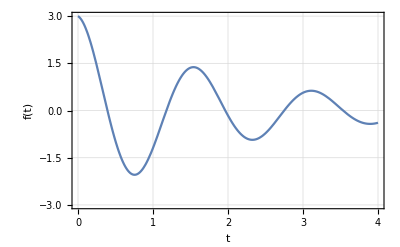

```mathematica
Plot[f[t],{t,0,4},Frame->True,FrameLabel->{"t","f(t)"},FrameStyle->Medium,GridLines->Automatic,PlotRange->{-3,3}]
```

```mathematica
g[t_]=2/(1+t^2)
```

2/(t^2+1)

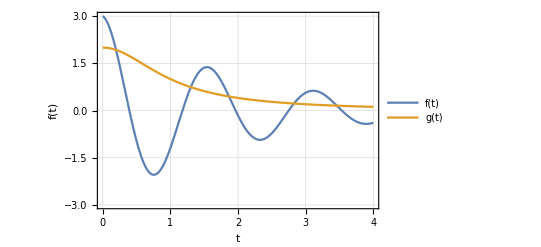

```mathematica
Plot[{f[t],g[t]},{t,0,4},Frame->True,FrameLabel->{"t","f(t)"},FrameStyle->Medium,GridLines->Automatic,PlotRange->{-3,3},PlotLegends->"Expressions"]
```

#### Trig manipulation

```mathematica
Cos[x+y]
```

cos(x+y)

```mathematica
TrigExpand[Cos[x+y]]
```

cos(x) cos(y)-sin(x) sin(y)

```mathematica
TrigReduce[TrigExpand[Cos[x+y]]]
```

cos(x+y)

```mathematica
Cos[2x]
```

cos(2 x)

```mathematica
TrigExpand[Cos[2x]]
```

cos^2(x)-sin^2(x)

```mathematica
TrigReduce[Cos[x]^7]
```

1/64 (35 cos(x)+21 cos(3 x)+7 cos(5 x)+cos(7 x))

```mathematica
TrigExpand[Cos[3x]+Cos[5x]]
```

cos^5(x)+cos^3(x)-10 sin^2(x) cos^3(x)+5 sin^4(x) cos(x)-3 sin^2(x) cos(x)

#### Indefinite integral

```mathematica
Integrate[Cos[7x]Exp[-3x]x^4,x]
```

1/41022298 ⅇ^(-3 x) (7 (707281 x^4+292668 x^3-55506 x^2-41760 x-2406) sin(7 x)+(-2121843 x^4+1951120 x^3+1044522 x^2+14268 x-34542) cos(7 x))

```mathematica
Integrate[x ArcTan[x]Log[x],x]
```

1/4 (-ⅈ 2-ⅈ x+ⅈ 2ⅈ x+x^2 (-tan^-1(x))+2 x^2 log(x) tan^-1(x)+3 x-2 x log(x)-tan^-1(x)+2 log(x) tan^-1(x))

```mathematica
Integrate[x ArcSin[x], x]
```

1/4 (√(1-x^2) x+(2 x^2-1) sin^-1(x))

#### Definite integral

```mathematica
Integrate[Cos[7x]Exp[-3x]x^4,{x,0,1}]
```

(34542 ⅇ^3+6301939 sin(7)+853525 cos(7))/(41022298 ⅇ^3)

```mathematica
Integrate[Cos[7x]Exp[-3x]x^4,{x,0,Infinity}]
```

17271/20511149

```mathematica
Integrate[Log[x],{x,0,1}]
```

-1

```mathematica
Integrate[1/(5+4Cos[x]),{x,0,2Pi}]
```

(2 π)/3

```mathematica
Exp[Cos[x]]
```

ⅇ^(cos(x))

```mathematica
Integrate[Exp[Cos[x]],{x,0,2Pi}]
```

2 π 01

```mathematica
f[x_]=1/(x+2)/(x+1)/(x^2+4)/(x+3)^2
```

1/((x+1) (x+2) (x+3)^2 (x^2+4))

```mathematica
Apart[f[x]]
```

(-3 x-82)/(6760 (x^2+4))+1/(20 (x+1))-1/(8 (x+2))+51/(676 (x+3))+1/(26 (x+3)^2)

```mathematica
Series[Exp[-x]Cos[x^2],{x,0,10}]
```

1-x+x^2/2-x^3/6-(11 x^4)/24+(59 x^5)/120-(179 x^6)/720+(419 x^7)/5040+(841 x^8)/40320-(13609 x^9)/362880+(73081 x^10)/3628800+O(x^11)

```mathematica
Series[Sqrt[1+x]x^2Cos[x],{x,0,10}]
```

x^2+x^3/2-(5 x^4)/8-(3 x^5)/16+(25 x^6)/384+(13 x^7)/768-(349 x^8)/46080+(401 x^9)/92160-(44047 x^10)/10321920+O(x^11)

```mathematica
Series[ArcTan[x]Cos[x]Exp[Exp[x]],{x,0,20}]
```

ⅇ x+ⅇ x^2+(ⅇ x^3)/6+(ⅇ x^5)/5+(53 ⅇ x^6)/360-(149 ⅇ x^7)/1680-(529 ⅇ x^8)/5040+(6793 ⅇ x^9)/120960+(10049 ⅇ x^10)/151200-(81371 ⅇ x^11)/1330560-(2618723 ⅇ x^12)/39916800+(282824177 ⅇ x^13)/6227020800+(2268044123 ⅇ x^14)/43589145600-(54850774547 ⅇ x^15)/1307674368000-(847838093 ⅇ x^16)/18162144000+(3248911161679 ⅇ x^17)/88921857024000+(14610562398083 ⅇ x^18)/355687428096000-(121626975633823 ⅇ x^19)/3686215163904000-(22498396242837049 ⅇ x^20)/608225502044160000+O(x^21)